# Functions Part 1

## Basic Exercises

### Question Subsection

Write a function mySum that returns the sum of two given numbers.

#### Solution

```mathematica
mySum[a_,b_]:=a+b
```

```mathematica
mySum[3,4]
```

7

### Question Subsection

Write a function mySum that returns the sum of any number of numbers. You can use the function Total to accomplish this.

#### Solution

```mathematica
mySum[a__]:=Total[{a}]
```

```mathematica
mySum[1,2,3]
```

6

### Question Subsection

Write a function separate that given a number will return it framed in with a light red background for positive integers, light blue background for negative integers and yellow for any other number.

#### Solution

```mathematica
separate[a_Integer?Positive]:=Framed[a,Background->LightRed]
separate[a_Integer?Negative]:=Framed[a,Background->LightBlue]
separate[a_Real]:=Framed[a,Background->Yellow]
```

```mathematica
separate[2]
```

2

```mathematica
separate[-2]
```

-2

```mathematica
separate[-2.2]
```

-2.2

### Question Subsection

Modify your function above so that it can also accept lists and apply the transformation to each element in the list. Test it on the following list.

```mathematica
mylist={-2,3.4,53,-3.33,4.4,23,82,34.5,-2.2,-9};
```

#### Solution

```mathematica
separate[x_List]:=Table[separate[n],{n,x}]
```

```mathematica
separate[mylist]
```

{-2,3.4,53,-3.33,4.4,23,82,34.5,-2.2,-9}

## Intermediate Exercises

### Question Subsection

Define a function trigPlot[fun_, num_] that takes one of the function Cos, or Sin and plots num number of plots whose frequencies vary from 1 to num, in increments of 1. Make it so that by default, the function plots three curves.

#### Hint

Frequency of a function is the parameter multiplying the argument. For example f is the frequency in Sin[f*x].

#### Solution

```mathematica
trigPlot[fun_,num_]:=Show[Table[Plot[fun[n*x],{x,0,10},PlotStyle->{RGBColor[{n/num,1-n/num,1}]}],{n,1,num,1}]]
trigPlot[fun_]:=trigPlot[fun,3]
```

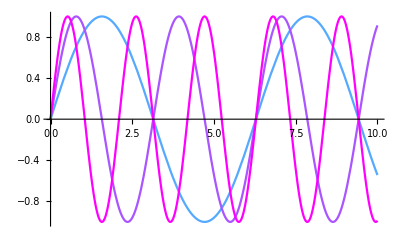

```mathematica
trigPlot[Sin]
```

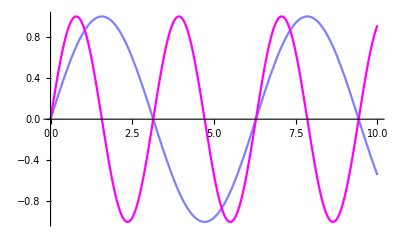

```mathematica
trigPlot[Sin,2]
```

### Question Subsection

Write a function that given a name, will print a summary of the person including their age, state in which they live, and their gender.

```mathematica
DataBase={
"Jalanda"->{"Age"-> 27,"State"->"PA", "Gender"->"F"},
"Jack"->{"Age"-> 54,"State"->"CA", "Gender"->"M"},
"Jake"->{"Age"-> 34,"State"->"MD", "Gender"->"M"},
"Jane"->{"Age"-> 14,"State"->"PA", "Gender"->"F"},
"Jeremiah"->{"Age"-> 57,"State"->"PA", "Gender"->"M"},
"Jodie"->{"Age"-> 39,"State"->"FL", "Gender"->"F"},
"Joe"->{"Age"-> 37,"State"->"PA", "Gender"->"M"},
"John"->{"Age"-> 23,"State"->"IL", "Gender"->"M"},
"Judy"->{"Age"-> 43,"State"->"PA",  "Gender"->"F"}
};
```

#### Hint

Use the Print function.

#### Solution

```mathematica
report[person_]:=(
data=person/.DataBase;
age="Age"/.data;
state="State"/.data;
gender="Gender"/.data;
Print[Row[{"name:",person}]];
Print[Row[{"Age:",age}]];
Print[Row[{"State:",state}]];
Print[Row[{"Gender:",gender}]];
)
```

```mathematica
report["John"]
```

name:John

Age:23

State:IL

Gender:M

```mathematica
report["Judy"]
```

name:Judy

Age:43

State:PA

Gender:F

## Advanced Exercises

### Question Subsection

Write a function that takes a list of length three {a,b,c} which represents the coefficients of a quadratic equation a x^2+b x+c=0 and returns the roots of the equation in a list of length two. 
You can find the roots as follows:

x_1= (-b + √(b^2- 4a c))/(2 a)
x_2= (-b - √(b^2- 4a c))/(2 a)

Your function should print out an error message in the list of numbers passed is invalid.

#### Solution

```mathematica
findroots[eq:{A_/;MatchQ[A,_Integer|_Real],B_/;MatchQ[B,_Integer|_Real],C_/;MatchQ[C,_Integer|_Real]}]:=
(a=eq[[1]];b=eq[[2]];c=eq[[3]];
x1 = (-b+Sqrt[b^2-4 a c])/(2 a);
x2 = (-b-Sqrt[b^2-4 a c])/(2 a);
{N[x1,2],N[x2,2]}
)
findroots[eq_]:=Print["Input must be a list of real valued numbers"]
```

```mathematica
findroots[3]
```

Input must be a list of real valued numbers

```mathematica
findroots[{3,1}]
```

Input must be a list of real valued numbers

```mathematica
findroots[{2,3,NotANumber}]
```

Input must be a list of real valued numbers

```mathematica
findroots[{1,2,3}]
```

{-1.+1.4 ⅈ,-1.-1.4 ⅈ}